```mathematica
Quit[]
```

```mathematica
SetDirectory[NotebookDirectory[]];
Import["mathematicaUtils.m"];
```

```mathematica
1931644749./10^9
```

1.93164

```mathematica
tims = {};
Do[
a=RandomPoly[55000,3];
b=RandomPoly[55000,3];
AppendTo[tims, Timing[Expand[a,b]][[1]] 10^9];
,{i,10}];
```

```mathematica
Mean[tims]
```

2.3397×10^7

```mathematica
55000^2/171424723.
```

17.6462

```mathematica
0.006145 10^9
```

6.145×10^6

```mathematica
Timing[Expand[a,b]][[1]] 10^9
```

2.17×10^6

```mathematica
tims = {};
Do[
a=RandomPoly[20000+RandomInteger[{0,132}],3];
b=RandomPoly[20000+RandomInteger[{0,132}],3];
AppendTo[tims,Timing[Expand[a,b]][[1]]],{i,100}];
```

```mathematica
Mean[tims] 10^9
```

8.77193×10^6

```mathematica
250 2 4
```

2000

```mathematica
Factor[1+x^2+2x^3+3x^4+4x^5+3x^6+4x^7+3x^8+2x^9+x^10]
```

(1+x) (1-x+x^2) (1+x+x^2) (1-x+x^2+x^3+x^4+x^5)

```mathematica
Expand[(1+x^1+x^2+x^3+x^4+x^5)(1-1x^1+x^2+x^3+x^4+x^5)]
```

1+x^2+2 x^3+3 x^4+4 x^5+3 x^6+4 x^7+3 x^8+2 x^9+x^10

```mathematica
RandomPoly[100,2]
```

-1+x-x^3-2 x^4-x^5+x^6-2 x^9+2 x^10+x^12-x^13-2 x^14-x^15-2 x^16-x^17-2 x^19+x^21-2 x^22-x^23-x^24-x^25-2 x^27+x^28-x^30+x^32-x^33-2 x^34+x^35+x^36+x^37-x^39-2 x^40-x^41-2 x^42-x^43+x^44-x^45-2 x^46+2 x^47+x^48+x^49+2 x^50-x^51+x^54+2 x^55-x^56-2 x^58+x^59+x^60-x^61+x^62+2 x^63+x^64+x^65-x^66+2 x^68-x^69-2 x^70+2 x^72+2 x^73-2 x^74-2 x^75-x^76+2 x^77-2 x^78-2 x^79-x^81-2 x^82+x^84-x^85-2 x^86+x^87+2 x^88-2 x^89-2 x^90-x^91+x^92-2 x^93-x^94-x^95+x^97+2 x^98-x^99-2 x^100

```mathematica
(* Generate data for distinct-degree factorization test *)
timings = GenerateRandomDistinctFactorizationData[
"../src/test/resources/cc/r2/core/polynomial/DistinctDegreeFactorizationSmall",
 100000, 123314,4,3,6,1000,100]
```

```mathematica
Median[timings] 10^9
```

252000.

```mathematica
timings1 = 
GenerateRandomDistinctFactorizationData[
"../src/test/resources/cc/r2/core/polynomial/DistinctDegreeFactorizationLarge",
 1000, 123314,8,5,15,10000,1000];
```

```mathematica
Max[timings1] 10^9
```

1.3504×10^7

```mathematica
timings2 = 
GenerateRandomDistinctFactorizationData[
"../src/test/resources/cc/r2/core/polynomial/DistinctDegreeFactorizationHuge",
 100, 123314,20,20,25,100000,10000];
```

```mathematica
Mean[timings2] 10^9
```

5.59528×10^7

```mathematica
200*200
```

```mathematica
thrs={0,100,200,300,400,500,600,700,800,900,1000,1100,1200,1300,1400,1500,1600,1700,1800,1900,2000,2100,2200,2300,2400,2500,2600,2700,2800,2900,3000,3100,3200,3300,3400,3500,3600,3700,3800,3900,4000,4100,4200,4300,4400,4500,4600,4700,4800,4900,5000,5100,5200,5300,5400,5500,5600,5700,5800,5900,6000,6100,6200,6300,6400,6500,6600,6700,6800,6900,7000,7100,7200,7300,7400,7500,7600,7700,7800,7900,8000,8100,8200,8300,8400,8500,8600,8700,8800,8900,9000,9100,9200,9300,9400,9500,9600,9700,9800,9900,10000,10100,10200,10300,10400,10500,10600,10700,10800,10900,11000,11100,11200,11300,11400,11500,11600,11700,11800,11900,12000,12100,12200,12300,12400,12500,12600,12700,12800,12900,13000,13100,13200,13300,13400,13500,13600,13700,13800,13900,14000,14100,14200,14300,14400,14500,14600,14700,14800,14900,15000,15100,15200,15300,15400,15500,15600,15700,15800,15900,16000,16100,16200,16300,16400,16500,16600,16700,16800,16900,17000,17100,17200,17300,17400,17500,17600,17700,17800,17900,18000,18100,18200,18300,18400,18500,18600,18700,18800,18900,19000,19100,19200,19300,19400,19500,19600,19700,19800,19900,20000,20100,20200,20300,20400,20500,20600,20700,20800,20900,21000,21100,21200,21300,21400,21500,21600,21700,21800,21900,22000,22100,22200,22300,22400,22500,22600,22700,22800,22900,23000,23100,23200,23300,23400,23500,23600,23700,23800,23900,24000,24100,24200,24300,24400,24500,24600,24700,24800,24900,25000,25100,25200,25300,25400,25500,25600,25700,25800,25900,26000,26100,26200,26300,26400,26500,26600,26700,26800,26900,27000,27100,27200,27300,27400,27500,27600,27700,27800,27900,28000,28100,28200,28300,28400,28500,28600,28700,28800,28900,29000,29100,29200,29300,29400,29500,29600,29700,29800,29900,30000,30100,30200,30300,30400,30500,30600,30700,30800,30900,31000,31100,31200,31300,31400,31500,31600,31700,31800,31900,32000,32100,32200,32300,32400,32500,32600,32700,32800,32900,33000,33100,33200,33300,33400,33500,33600,33700,33800,33900,34000,34100,34200,34300,34400,34500,34600,34700,34800,34900,35000,35100,35200,35300,35400,35500,35600,35700,35800,35900,36000,36100,36200,36300,36400,36500,36600,36700,36800,36900,37000,37100,37200,37300,37400,37500,37600,37700,37800,37900,38000,38100,38200,38300,38400,38500,38600,38700,38800,38900,39000,39100,39200,39300,39400,39500,39600,39700,39800,39900,40000,40100,40200,40300,40400,40500,40600,40700,40800,40900,41000,41100,41200,41300,41400,41500,41600,41700,41800,41900,42000,42100,42200,42300,42400,42500,42600,42700,42800,42900,43000,43100,43200,43300,43400,43500,43600,43700,43800,43900,44000,44100,44200,44300,44400,44500,44600,44700,44800,44900,45000,45100,45200,45300,45400,45500,45600,45700,45800,45900,46000,46100,46200,46300,46400,46500,46600,46700,46800,46900,47000,47100,47200,47300,47400,47500,47600,47700,47800,47900,48000,48100,48200,48300,48400,48500,48600,48700,48800,48900,49000,49100,49200,49300,49400,49500,49600,49700,49800,49900,50000,50100,50200,50300,50400,50500,50600,50700,50800,50900,51000,51100,51200,51300,51400,51500,51600,51700,51800,51900,52000,52100,52200,52300,52400,52500,52600,52700,52800,52900,53000,53100,53200,53300,53400,53500,53600,53700,53800,53900,54000,54100,54200,54300,54400,54500,54600,54700,54800,54900,55000,55100,55200,55300,55400,55500,55600,55700,55800,55900,56000,56100,56200,56300,56400,56500,56600,56700,56800,56900,57000,57100,57200,57300,57400,57500,57600,57700,57800,57900,58000,58100,58200,58300,58400,58500,58600,58700,58800,58900,59000,59100,59200,59300,59400,59500,59600,59700,59800,59900,60000,60100,60200,60300,60400,60500,60600,60700,60800,60900,61000,61100,61200,61300,61400,61500,61600,61700,61800,61900,62000,62100,62200,62300,62400,62500,62600,62700,62800,62900,63000,63100,63200,63300,63400,63500,63600,63700,63800,63900,64000,64100,64200,64300,64400,64500,64600,64700,64800,64900,65000,65100,65200,65300,65400,65500,65600,65700,65800,65900,66000,66100,66200,66300,66400,66500,66600,66700,66800,66900,67000,67100,67200,67300,67400,67500,67600,67700,67800,67900,68000,68100,68200,68300,68400,68500,68600,68700,68800,68900,69000,69100,69200,69300,69400,69500,69600,69700,69800,69900};
tims={0.3658248082583115,1.3476536916293422,1.8317245512799898,1.9048445861885828,1.9319375846855882,2.1510426631556907,2.1059143570407763,2.0738269002788803,2.1367259490047483,2.1021396338042946,2.1452504327065114,2.2266063352245067,2.1562168820834056,2.03421684677929,2.1133499220098275,2.0874539842448026,2.1432883363054525,2.170505398389476,2.2071661405724305,2.099455269697628,2.037807775785271,2.104939149134135,2.05030535563228,2.149821554880745,2.1506905692407536,2.1781381352778184,2.058476459220826,2.1358958089475126,2.199791171538459,2.223491359844248,2.1847615209285327,2.225211660711498,2.1451622095534737,2.220038363182367,2.1616063693694376,2.13783959010041,2.1671099177952993,2.050250039076359,2.0379798004470144,2.1786749388576467,2.1186582386214563,2.181723482118824,2.1748087281338,2.1988155342630713,2.126113549865356,2.2195028945188953,2.238077614821728,2.1286326761545564,2.1326467930997914,2.0423681074494278,2.2337154011893787,2.2086551670883807,2.1450126452660783,2.1615885824923073,2.1393726310394405,2.25981504347957,2.1873575297497387,2.1361737658962423,2.186672661667653,2.2784439855063185,2.3442732761827836,2.2022745413613256,2.1544999245531735,2.04531115336349,2.031441498368964,2.048840129333868,1.869794619845152,1.8994510099920432,1.8805556731835045,1.7960889013443848,1.8380599526114616,1.8214030432053225,1.8680090170296344,1.7968553355748589,1.8002605509916805,1.8143713847310974,1.850784878394822,1.8902623780890968,1.8623273350026244,1.8299003801660176,1.8232846512769878,1.7598177159277562,1.8079922692722266,1.7405300086884274,1.8574695620266828,1.8611572715427915,1.7689767770824656,1.7914104282538703,1.8929550018641714,1.8332175628123761,1.8864347613502637,1.83564456525355,1.8405290353781736,1.8521764716663403,1.783351043109975,1.7971598950681047,1.7060183747209487,1.742030352467229,1.8087255892070877,1.7701038173421109,1.772546701130357,1.7791290966885742,1.7699760847143742,1.8364182574881265,1.8283334065456922,1.8542019438531088,1.857516753695792,1.8079116163266433,1.873537399135253,1.8235301869452645,1.8250081752768037,1.8458897123232223,1.8693662507726956,1.83868662277274,1.8878263832463316,1.9099184247879244,1.8468636623064583,1.811726390886512,1.9350149961690737,1.8457359407450948,1.854485872141689,1.8455164512362197,1.9585433404593435,1.796481724426285,1.855983384474556,1.8718423707751457,1.8560851034884367,1.8962828101406397,1.8738412117965126,1.840027261637999,1.8774433469799015,1.966265617015186,1.8047198192183949,1.8524426667739116,1.9281519619146927,1.783166533104646,1.8229499934922953,1.8661832691544153,1.86127038213213,2.023238743183723,1.8725393498623903,1.8704953791177799,1.8841265688556288,1.8802189135215697,1.9119926326312264,1.8551271917026995,1.8360864526154816,1.8333605098243224,1.8312194976102325,1.8735427203893424,1.8797774708575097,1.7951553046479198,1.8104007622815548,1.9013282644815988,1.8776273610994696,1.8628544817670647,1.867353908742581,1.868575640319658,1.814397470807732,1.838862027461695,1.858981591660666,1.8889808727676634,1.9168399282336859,1.8677295827718858,1.7560140990971023,1.8157114168012898,1.894839927400277,1.92736438704937,1.8475928426260222,1.8767023815522825,1.9062697387663106,1.9043606043352637,1.83894775425189,1.8024082541205702,1.8348915503576786,1.7801595916605566,1.93137554317834,1.788751508387654,1.9059160679866807,1.8752019018728099,1.8972882750535611,1.8953512886931225,1.8468028919958697,1.8651506995094425,1.906855812440377,1.9192045122235633,1.8247119301176555,1.7965539636356358,1.9003424377985039,1.8410761882733675,1.8980306379748724,1.8811588879258712,1.954194614237942,1.8426400408860057,1.806327475360752,1.8221921974017166,1.926663733731263,1.8778374296657683,1.9074929539856131,1.8506254790888166,1.8803660293026994,1.8359826656459777,1.8304860588100884,1.9344322239997513,1.8801710525726036,1.9092128686722936,1.7945355630875246,1.9502705631743893,1.8868345871200591,1.8940855698836305,1.8842612631439752,1.8566829526194166,1.873606011186921,1.876747093311639,1.8968866386837342,1.858119531033416,1.8507077209533644,1.8987831299339686,1.8634764059193862,1.8367139805769526,1.875241258755803,1.8683640251156917,1.8928115728992017,1.8533138300056198,1.850093081247224,1.8703126705649182,1.8898704463471199,1.8954680721251747,1.9573101906193904,1.8383368001626932,1.8256127096586283,1.9084585196639954,1.951181329800335,1.9286727179674743,1.912207980790319,1.8889603174681209,1.92208772560063,1.8934045028863788,1.9053691743181118,1.8499150736553394,1.9507922093777064,1.83287274992555,1.901480629568426,1.8623745504972888,1.9032866569419382,1.8781970313925733,1.9205720489217366,1.805278523280759,1.8893625546383277,1.8536339864860998,1.7634230087873721,1.7273139346372528,1.7992069650921967,1.6234096212748306,1.6658472322387237,1.6073599022753509,1.6005395881170206,1.683870717190469,1.6596316179251078,1.610358284617588,1.6273563745469324,1.6353816516979227,1.6807411752539743,1.6948493352503176,1.6786348568384866,1.629316242395926,1.6811569708559937,1.6273106036548883,1.7016121303756049,1.6148881022089079,1.6514877249932292,1.6003704861499812,1.7369182147105469,1.630711997253692,1.7129356617857783,1.625212418929525,1.66408033132673,1.6407381663977252,1.6453328676022443,1.625263991982895,1.6092994316896188,1.5870126559314588,1.6850639037420971,1.6326492041221132,1.656884477536151,1.6875790476173589,1.662419703680157,1.6949499424548073,1.6800973827197798,1.6481055542207945,1.626215177663017,1.6926294050960027,1.652482792530713,1.640021536799728,1.6299968237311044,1.6647566668428337,1.6360626516602395,1.606370219131413,1.6232247444830041,1.6883790055737138,1.6123428131742419,1.5885050512008623,1.7694469281063054,1.6514377109835474,1.6200191349065811,1.6667815959576742,1.6190304215980897,1.6155766970299839,1.5794481869055994,1.6312885141432303,1.6669160263847937,1.603650808606386,1.7181938329611073,1.646146479662314,1.6406495664575758,1.6051024722117608,1.6966072258021654,1.644467437435229,1.6210109079122745,1.6433448600882405,1.6903653627912587,1.6537712695714233,1.7292933619063238,1.5803101983105003,1.677587972709084,1.6146846566618474,1.6505029618593197,1.653477252462466,1.6562456992171397,1.6455244849762172,1.6129255246536764,1.6058477118337136,1.720607368793411,1.6144403516988128,1.668117004224025,1.6847767533841576,1.6212252931713607,1.6691341700210058,1.6620257096553606,1.6614594598418813,1.6221696593851143,1.6685614887652478,1.7093347015443223,1.647627186036407,1.7065817713539204,1.6582880159485487,1.6386201317404772,1.588173817908864,1.623209438795976,1.6582610547974914,1.634048377926419,1.6859101572085944,1.6630296825988502,1.6404531482819655,1.57561840049316,1.6664630224806976,1.4946173224811385,1.6748197930933852,1.6204712213211356,1.645597031618176,1.6555958712855523,1.675116994509414,1.7220278550663852,1.5810253821178988,1.6820102125276968,1.570297918546967,1.5920110955657878,1.6100941101838955,1.6848561751445825,1.7397464466000407,1.6199078137246583,1.6763494376895132,1.7857922067616894,1.612919600309716,1.6116867400656594,1.6141856631152138,1.6641667296018816,1.614035235153836,1.6261141658482328,1.6780541424621693,1.6788683928113781,1.629596616328055,1.7642284484350834,1.6275671578893935,1.613632501822311,1.683677000692794,1.6155442807364027,1.6314752441639195,1.7168841951908915,1.594523518624761,1.5975872158874043,1.5517213893311774,1.7591617630461276,1.6313457236358524,1.6723670662961299,1.652500163296201,1.5825977021210058,1.6540767631676512,1.6496484349966816,1.5974023099909818,1.6451459919868947,1.613513250402982,1.685715847856366,1.6605526069867411,1.5591234708576243,1.6372086397663461,1.6242596001441874,1.6393632771357038,1.6354102241966901,1.629484874136719,1.6398926841330344,1.6674553748610497,1.6405996287222102,1.6836463843028175,1.6672649629967322,1.6388811372506902,1.6499031518486302,1.6236434651913374,1.6720376912357096,1.6271544597950836,1.703091257301873,1.6846667759444163,1.6663775897736655,1.6498258446047676,1.6919193325367865,1.6084701582706549,1.6713832808378235,1.6309741324881313,1.6592391665167354,1.6839033039463314,1.6394174044591803,1.6232211361585829,1.7055057579001331,1.6004708114310577,1.6291323096807715,1.6820779468842957,1.6065893462430467,1.6142504693276767,1.6819019669658664,1.6307914870080775,1.6639563920193012,1.7041748065913132,1.6953813965695061,1.6174175118557046,1.6516573346401937,1.62368989834805,1.616074615173224,1.7133214885174437,1.629506033656233,1.6030511014481275,1.5899787170503321,1.7979856527163607,1.7055252746375198,1.6832963866228532,1.6612518457744245,1.6039159025408671,1.6031225213478415,1.6303374266998312,1.7441849774877565,1.8624514573398403,1.6450387699392737,1.669391998499967,1.6720694633915651,1.6095549145724852,1.6229181351921997,1.6415254961051466,1.622014310431568,1.6172677172131396,1.6806555856860115,1.6097044705050498,1.5909752445749907,1.6788262712273492,1.669000775042734,1.6341338405869572,1.7039606749225709,1.647185951428477,1.6250954026166349,1.6232754078087521,1.6463218255775063,1.6542269431907175,1.624474612340295,1.592373121680625,1.6727562308863055,1.605948759468319,1.6235609358481935,1.567946855405492,1.6265941638352286,1.6849876369459842,1.6389133587325575,1.578358224971689,1.6719451762690147,1.6404010264689264,1.6572798121056338,1.6520442903335635,1.6621921945782019,1.5960705841774423,1.5571314556570088,1.6229093671169574,1.6361372563049983,1.6499379514510053,1.5842126585692662,1.6312626162818693,1.6677742572122471,1.6563659768237644,1.6600045972181359,1.6220350886683501,1.6699697388825034,1.6108393013008657,1.6292151740643905,1.585468983110249,1.5815646674238686,1.6976226186851133,1.7650383565078576,1.6215182933542753,1.6537251492025722,1.6389736442815097,1.6008651633583018,1.6757637009631265,1.6292398578572787,1.7198625552155113,1.6885298690512316,1.6031279136036962,1.6902299943461891,1.6494683648597248,1.6221914111076323,1.6031556518908219,1.6002029528795505,1.6003663714934557,1.6153544205052204,1.6560101842343515,1.625314905921419,1.682750409428251,1.6581041952424973,1.687277853429618,1.6384755014160213,1.607941547684644,1.5831538182871931,1.6325057908812715,1.6560442855292432,1.6565674572298035,1.6345034772018296,1.6150833590109301,1.6342869221381733,1.608127956740807,1.644449551210198,1.6217981483726736,1.679479716123495,1.6248939486415883,1.658434358244831,1.6423724921023877,1.6937931815982212,1.6370436943760078,1.632075648408112,1.6963805084144594,1.634189822323304,1.7111310278484797,1.6094852242755948,1.5958349565296648,1.659018457118678,1.6383174317191715,1.64225642593871,1.6140119419483743,1.6657798729344804,1.68518841756504,1.6180139502520907,1.607999585280415,1.6916455161132131,1.630734344584846,1.6553727549830828,1.5920194262458252,1.6687111944383333,1.704314240498783,1.6844219145431205,1.6376121934379926,1.641426443426157,1.6277592220983563,1.6332720871554038,1.6701319548640698,1.6017928695588257,1.712468615203135,1.6118028738179744,1.619528996116234,1.669307326886302,1.6581835428986245,1.6052626331035755,1.6582967835253606,1.6357717021073077,1.629079346048786,1.586483318240632,1.6776651871580597,1.6233350694089543,1.655198759830252,1.6260849580617371,1.7141725928391465,1.6038924423836243,1.6879828331105582,1.644671160932349,1.6322139959513686,1.5767230829817618,1.6395225583336122,1.6679687608588039,1.5869125264925747,1.6473995898298035,1.7058672981626264,1.633511255705583,1.6754444889205504,1.7773974947628672,1.6431549380292876,1.678539112210951,1.6296778739234536,1.6791445499536453,1.6261512104426492,1.6430326831110982,1.6858250569226674,1.62569286241691,1.618809447557461,1.6296200390804654,1.634771675908577,1.5462092670029182,1.6577894404706677,1.6486478074987152,1.5825488372280392,1.7927337321602628,1.658593176660926,1.6664058585462715,1.588743091631861,1.659710777504127,1.6500165264792461,1.6802090323587229,1.635978628192063,1.6185833759972905,1.6784321297609794,1.7124130041095817,1.6076109790464304,1.6593102095105516,1.6619329878544784,1.6248127924009867,1.6352286300194263,1.6624530461244158,1.6609119738440006,1.5952471997820956,1.666379857720373,1.668527465357463,1.599421697026931,1.645729979075067,1.6632564948612087,1.685695954524818,1.6258281834561714,1.5939949549748316,1.682821754595438,1.5771436572449642,1.6450225387494963,1.5969771005450215,1.6195479126631265,1.6019746564318262,1.6352962945013805,1.6657188936131846,1.5468821328509321,1.613842967377848,1.6689328856335768,1.5577445549645954,1.6487038921818291,1.7505601493411336,1.5943093940955033,1.5977145138017461,1.5783189269426257,1.5813275612324558,1.635315604431135,1.6322513468731346,1.5605487974878367,1.6881995809269161,1.6035028231494979,1.730276908923721,1.6952109857869813,1.7024466100002484,1.657354582612597,1.696775372414162,1.5765492736697924,1.6274304148413017,1.6714825917257161,1.6567075338394468,1.7063705628799581,1.647302546417111,1.6407315203300723,1.5965230155094048,1.5962168048050505,1.7041306604804798,1.7808247628516967,1.772601372998659,1.7813751310566122,1.69591809854379,1.6441613093860419,1.6414431541710013,1.6715111709182737,1.7068440434197143,1.8221797603714898,1.919732783733475,1.6630994587424413,1.7247538579937232,1.6641658817223923};
```

```mathematica
thrs={0,1000,2000,3000,4000,5000,6000,7000,8000,9000,10000,11000,12000,13000,14000,15000,16000,17000,18000,19000,20000,21000,22000,23000,24000,25000,26000,27000,28000,29000,30000,31000,32000,33000,34000,35000,36000,37000,38000,39000,40000,41000,42000,43000,44000,45000,46000,47000,48000,49000,50000,51000,52000,53000,54000,55000,56000,57000,58000,59000,60000,61000,62000,63000,64000,65000,66000,67000,68000,69000};
tims={0.9724155184240713,4.36534133647328,4.3094032703493355,4.688109176268387,4.578903831194015,4.531230938272474,4.678845761814311,3.6309602189282977,3.810156270089168,3.9378126127567787,4.0377969426866525,4.196567132425965,4.254926491167822,3.6837569049201875,4.305839830829546,4.1162149590134955,3.650705596939855,3.8559126211925117,3.687754511572008,3.698542568923554,3.958608516746037,3.622185994538134,3.92776967689235,3.9946191656817067,3.893795944028279,3.6501221603358545,3.638250548039086,3.223077257751798,3.012600444431138,3.134336725420463,3.206284438463342,3.295782723444953,3.4009757336407658,3.23923663700901,3.4583214927741484,3.042820972046181,3.256868412381998,3.1889175822009133,3.3667761542369368,2.999238910908188,3.2910468376142425,3.1855348572792557,3.1397863093071163,3.331059506747293,3.2235023271466208,3.1863026425129988,3.2854467622820023,3.505098710501828,3.2368050954836978,2.841340979936894,3.1597572472811475,3.188729813287236,3.358578796044323,3.579678948103593,3.4123163185413325,3.3219756328537358,3.379003268504981,3.1590703384693732,3.199121184238181,3.2455158109093656,3.271373632773317,3.263452789869203,3.1292240194559193,3.309337519000851,3.152523659884506,3.5108245154523914,2.9605322686983735,3.356347248895226,3.2372212788644634,3.203689025338669};
```

```mathematica
Mean[ConstantArray[4,6]~Join~ConstantArray[5,47-6]]//N
```

4.87234

```mathematica
47 3/4.
```

35.25

```mathematica
Sqrt[5500.]
```

74.162

```mathematica
polyData = {6650,68859,22275,45078,86304,9759,77160,70073,41899,52881,62889,58468,35826,60356,67213,66957,48370,17669,9933,85458,3134,76771,30441,33067,35939,15710,2403,8585,55218,72652,23952,85278,92366,81522,47437,32453,19760,5051,84527,55625,38211,18165,38887,94661,4046,88205,91932,42789,41182,33497,57403,82501,35133,2346,35376,92459,69637,50572,31966,5279,33814,11215,30244,39497,82716,36040,25972,16361,88885,89514,66641,78008,88470,51393,5626,54147,24953,48299,77990,74869,22067,94204,11658,30396,61221,28882,24978,11737,79083,52379,45547,7482,89156,84783,13140,38412,10110,72974,74516,75284,25327,66808,54726,3462,53452,56885,5921,68793,33047,39883,49840,67584,13360,43291,19317,39530,5922,39463,86786,15846,21785,40463,83277,74177,41218,14196,51191,43599,23830,87613,1414,27672,32990,81745,52957,27855,71616,93334,65928,8242,92984,8345,17228,59512,35349,28330,19021,39366,85001,22699,10186,27312,42484,62155,65370,14172,68282,61633,10726,84239,66430,15752,90164,81410,79784,5751,45762,78313,27020,37809,2897,15129,14970,24014,81092,53643,88663,42889,84295,18189,59806,91795,88777,50017,38189,41721,50622,89687,54431,54986,20530,68806,44449,62479,34149,55409,59757,54592,3636,22578,36217,22896,38901,38573,68767,38291,13457,64421,28767,16589,51589,12948,45939,26680,48003,43471,7013,37294,25587,51820,65336,25703,93341,59022,76069,48653,41795,41392,48562,26240,76813,76274,3876,56383,57752,24556,76413,87271,84231,67364,49656,59996,20438,66506,43313,57650,80206,36887,17852,77602,81316,61562,33687,78752,43969,73349,65202,10234,10062,51956,87369,66206,82705,70217,74172,34581,94543,7664,24364,18110,66448,1};
```

```mathematica
poly = Plus@@Table[x^i polyData[[i+1]],{i,0,Length[polyData]-1}];
```

```mathematica
Timing[Factor[poly,Modulus->5659]]
```

{0.162102,(4324+2713 x+2712 x^2+4484 x^3+1869 x^4+1384 x^5+452 x^6+4955 x^7+4523 x^8+4247 x^9+4261 x^10+4549 x^11+2584 x^12+x^13) (2496+1689 x+4455 x^2+3832 x^3+3440 x^4+4460 x^5+230 x^6+5212 x^7+536 x^8+4561 x^9+5297 x^10+3522 x^11+4519 x^12+443 x^13+2002 x^14+5102 x^15+3591 x^16+529 x^17+231 x^18+5569 x^19+3015 x^20+2299 x^21+1895 x^22+654 x^23+81 x^24+3758 x^25+595 x^26+1133 x^27+1697 x^28+3730 x^29+4502 x^30+2271 x^31+3799 x^32+3863 x^33+4352 x^34+2636 x^35+721 x^36+4764 x^37+3678 x^38+3360 x^39+2261 x^40+1493 x^41+1281 x^42+3212 x^43+3249 x^44+5056 x^45+4910 x^46+4009 x^47+4754 x^48+5412 x^49+2278 x^50+533 x^51+3451 x^52+872 x^53+1650 x^54+232 x^55+1086 x^56+3610 x^57+3456 x^58+617 x^59+1711 x^60+3514 x^61+3576 x^62+2991 x^63+4208 x^64+3304 x^65+524 x^66+2346 x^67+2804 x^68+442 x^69+3990 x^70+4256 x^71+91 x^72+835 x^73+2437 x^74+3989 x^75+3630 x^76+2983 x^77+4448 x^78+2832 x^79+2325 x^80+1259 x^81+3502 x^82+5617 x^83+3277 x^84+5376 x^85+2694 x^86+5574 x^87+2544 x^88+619 x^89+1660 x^90+4599 x^91+3915 x^92+4073 x^93+1076 x^94+1142 x^95+5421 x^96+1417 x^97+2775 x^98+922 x^99+224 x^100+1417 x^101+3362 x^102+1497 x^103+257 x^104+801 x^105+5047 x^106+4687 x^107+29 x^108+1604 x^109+3890 x^110+1857 x^111+2642 x^112+4156 x^113+5117 x^114+5185 x^115+5334 x^116+1155 x^117+5301 x^118+2787 x^119+2035 x^120+1535 x^121+1744 x^122+4132 x^123+2620 x^124+1383 x^125+1912 x^126+4676 x^127+4427 x^128+3491 x^129+1472 x^130+2118 x^131+5491 x^132+1809 x^133+2240 x^134+5613 x^135+3625 x^137+2323 x^138+1881 x^139+838 x^140+3429 x^141+1548 x^142+3826 x^143+1743 x^144+3992 x^145+1134 x^146+4673 x^147+2195 x^148+176 x^149+4249 x^150+1132 x^151+3735 x^152+4022 x^153+4907 x^154+5185 x^155+2687 x^156+3625 x^157+4174 x^158+5363 x^159+1203 x^160+436 x^161+1711 x^162+596 x^163+2229 x^164+716 x^165+2668 x^166+4412 x^167+1368 x^168+1180 x^169+1327 x^170+3505 x^171+1977 x^172+3010 x^173+1404 x^174+1983 x^175+4693 x^176+2486 x^177+5 x^178+4830 x^179+5068 x^180+17 x^181+2287 x^182+2287 x^183+1626 x^184+530 x^185+962 x^186+4631 x^187+1362 x^188+1965 x^189+5444 x^190+2187 x^191+1257 x^192+2885 x^193+3990 x^194+3828 x^195+3211 x^196+5535 x^197+5553 x^198+2412 x^199+5001 x^200+5569 x^201+1855 x^202+3610 x^203+1292 x^204+3695 x^205+1616 x^206+4032 x^207+550 x^208+4008 x^209+3753 x^210+3891 x^211+1539 x^212+1805 x^213+2505 x^214+3371 x^215+495 x^216+3824 x^217+2675 x^218+1978 x^219+1657 x^220+1668 x^221+4812 x^222+2234 x^223+349 x^224+5429 x^225+2271 x^226+2844 x^227+2768 x^228+3118 x^229+3165 x^230+2500 x^231+2109 x^232+1334 x^233+1775 x^234+5096 x^235+1779 x^236+4162 x^237+2216 x^238+3511 x^239+5429 x^240+3367 x^241+5326 x^242+5119 x^243+5385 x^244+2155 x^245+2274 x^246+5343 x^247+3303 x^248+1282 x^249+524 x^250+2002 x^251+3010 x^252+4598 x^253+4252 x^254+1016 x^255+5425 x^256+1615 x^257+x^258)}

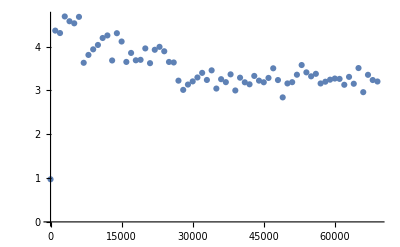

```mathematica
ListPlot[Transpose[{thrs,tims}](*Joined->True(*,PlotRange->{{1000,1500},Automatic}*)*)]
```

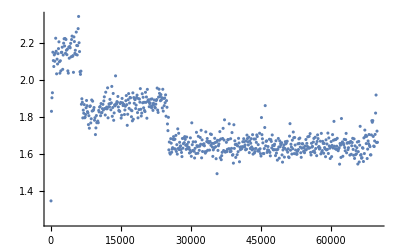

```mathematica
ListPlot[Transpose[{thrs,tims}](*Joined->True(*,PlotRange->{{1000,1500},Automatic}*)*)]
```

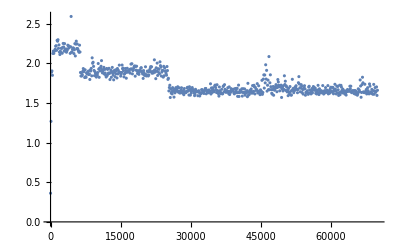

```mathematica
ListPlot[Transpose[{thrs,tims}](*Joined->True(*,PlotRange->{{1000,1500},Automatic}*)*)]
```

```mathematica
Prime[RandomInteger[{1,10000}]]
```

63577

```mathematica
Factor[x^2-1,Modulus->101]
```

(1+x) (100+x)

```mathematica
Factor[Sum[i+m,{i,0,n-m}]]
```

-1/2 (-1+m-n) (m+n)

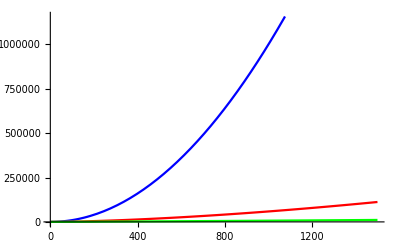

```mathematica
Plot[{x^2,x^1.59,x Log[x]},{x,1,1500}, PlotStyle->{Blue,Red,Green}]
```

```mathematica
Expand[(1+x+x^2+x^3)(1+x+x^2)]
```

1+2 x+3 x^2+3 x^3+2 x^4+x^5

```mathematica
Factor[991+951x^1+5298x^2+5465x^3+1419x^4+4100x^5+3593x^6+2165x^7+2286x^8+1950x^9+640x^10+1878x^11+1872x^12+3766x^13+4964x^14+4708x^15+3098x^16+692x^17+4274x^18+573x^19+3134x^20+3204x^21+2146x^22+4772x^23+1985x^24+4392x^25+2403x^26+2926x^27+4287x^28+4744x^29+1316x^30+393x^31+1822x^32+2296x^33+2165x^34+4158x^35+2783x^36+5051x^37+5301x^38+4694x^39+4257x^40+1188x^41+4933x^42+4117x^43+4046x^44+3320x^45+1388x^46+3176x^47+1569x^48+5202x^49+813x^50+3275x^51+1179x^52+2346x^53+1422x^54+1915x^55+1729x^56+5300x^57+3671x^58+5279x^59+5519x^60+5556x^61+1949x^62+5543x^63+3490x^64+2086x^65+3336x^66+5043x^67+4000x^68+4629x^69+4392x^70+4441x^71+3585x^72+462x^73+5626x^74+3216x^75+2317x^76+3027x^77+4423x^78+1302x^79+5090x^80+3660x^81+340x^82+2101x^83+4631x^84+587x^85+2342x^86+419x^87+5516x^88+1448x^89+275x^90+1823x^91+4271x^92+5557x^93+1822x^94+4458x^95+4451x^96+5066x^97+949x^98+1717x^99+2691x^100+4559x^101+3795x^102+3462x^103+2521x^104+295x^105+262x^106+885x^107+4752x^108+270x^109+4568x^110+5335x^111+2042x^112+3678x^113+2340x^114+5576x^115+263x^116+5509x^117+1901x^118+4528x^119+4808x^120+850x^121+4051x^122+610x^123+1605x^124+2878x^125+260x^126+3986x^127+1194x^128+2728x^129+1414x^130+5036x^131+4695x^132+2519x^133+2026x^134+5219x^135+3708x^136+2790x^137+3679x^138+2583x^139+2440x^140+2686x^141+251x^142+2922x^143+1395x^144+35x^145+2044x^146+5412x^147+116x^148+63x^149+4527x^150+4676x^151+2871x^152+5565x^153+3121x^154+2854x^155+374x^156+5043x^157+5067x^158+5013x^159+4181x^160+4434x^161+5279x^162+2184x^163+558x^164+92x^165+490x^166+4746x^167+4384x^168+3855x^169+2897x^170+3811x^171+3652x^172+1378x^173+1866x^174+2712x^175+3778x^176+3276x^177+5069x^178+1212x^179+3216x^180+1251x^181+3892x^182+4745x^183+4235x^184+2108x^185+5350x^186+4802x^187+3500x^188+4055x^189+3553x^190+898x^191+4836x^192+230x^193+195x^194+4478x^195+3167x^196+3661x^197+3636x^198+5601x^199+2263x^200+260x^201+4947x^202+4619x^203+859x^204+4337x^205+2139x^206+2172x^207+472x^208+5271x^209+658x^210+1630x^211+667x^212+4044x^213+2731x^214+3858x^215+1354x^216+3340x^217+2951x^218+889x^219+3087x^220+3067x^221+2797x^222+2432x^223+2502x^224+3381x^225+2182x^226+1779x^227+3290x^228+3604x^229+3246x^230+2707x^231+3876x^232+5452x^233+1162x^234+1920x^235+2846x^236+2386x^237+5005x^238+5115x^239+4384x^240+3406x^241+3461x^242+4257x^243+3700x^244+1060x^245+980x^246+2933x^247+875x^248+4035x^249+2090x^250+4972x^251+5392x^252+5185x^253+4356x^254+5441x^255+2953x^256+4575x^257+4403x^258+1025x^259+2484x^260+3957x^261+3479x^262+2309x^263+605x^264+627x^265+3999x^266+2005x^267+1728x^268+1133x^269+4199x^270+x^271
,Modulus->5659]//Timing
```

{0.167581,(4324+2713 x+2712 x^2+4484 x^3+1869 x^4+1384 x^5+452 x^6+4955 x^7+4523 x^8+4247 x^9+4261 x^10+4549 x^11+2584 x^12+x^13) (2496+1689 x+4455 x^2+3832 x^3+3440 x^4+4460 x^5+230 x^6+5212 x^7+536 x^8+4561 x^9+5297 x^10+3522 x^11+4519 x^12+443 x^13+2002 x^14+5102 x^15+3591 x^16+529 x^17+231 x^18+5569 x^19+3015 x^20+2299 x^21+1895 x^22+654 x^23+81 x^24+3758 x^25+595 x^26+1133 x^27+1697 x^28+3730 x^29+4502 x^30+2271 x^31+3799 x^32+3863 x^33+4352 x^34+2636 x^35+721 x^36+4764 x^37+3678 x^38+3360 x^39+2261 x^40+1493 x^41+1281 x^42+3212 x^43+3249 x^44+5056 x^45+4910 x^46+4009 x^47+4754 x^48+5412 x^49+2278 x^50+533 x^51+3451 x^52+872 x^53+1650 x^54+232 x^55+1086 x^56+3610 x^57+3456 x^58+617 x^59+1711 x^60+3514 x^61+3576 x^62+2991 x^63+4208 x^64+3304 x^65+524 x^66+2346 x^67+2804 x^68+442 x^69+3990 x^70+4256 x^71+91 x^72+835 x^73+2437 x^74+3989 x^75+3630 x^76+2983 x^77+4448 x^78+2832 x^79+2325 x^80+1259 x^81+3502 x^82+5617 x^83+3277 x^84+5376 x^85+2694 x^86+5574 x^87+2544 x^88+619 x^89+1660 x^90+4599 x^91+3915 x^92+4073 x^93+1076 x^94+1142 x^95+5421 x^96+1417 x^97+2775 x^98+922 x^99+224 x^100+1417 x^101+3362 x^102+1497 x^103+257 x^104+801 x^105+5047 x^106+4687 x^107+29 x^108+1604 x^109+3890 x^110+1857 x^111+2642 x^112+4156 x^113+5117 x^114+5185 x^115+5334 x^116+1155 x^117+5301 x^118+2787 x^119+2035 x^120+1535 x^121+1744 x^122+4132 x^123+2620 x^124+1383 x^125+1912 x^126+4676 x^127+4427 x^128+3491 x^129+1472 x^130+2118 x^131+5491 x^132+1809 x^133+2240 x^134+5613 x^135+3625 x^137+2323 x^138+1881 x^139+838 x^140+3429 x^141+1548 x^142+3826 x^143+1743 x^144+3992 x^145+1134 x^146+4673 x^147+2195 x^148+176 x^149+4249 x^150+1132 x^151+3735 x^152+4022 x^153+4907 x^154+5185 x^155+2687 x^156+3625 x^157+4174 x^158+5363 x^159+1203 x^160+436 x^161+1711 x^162+596 x^163+2229 x^164+716 x^165+2668 x^166+4412 x^167+1368 x^168+1180 x^169+1327 x^170+3505 x^171+1977 x^172+3010 x^173+1404 x^174+1983 x^175+4693 x^176+2486 x^177+5 x^178+4830 x^179+5068 x^180+17 x^181+2287 x^182+2287 x^183+1626 x^184+530 x^185+962 x^186+4631 x^187+1362 x^188+1965 x^189+5444 x^190+2187 x^191+1257 x^192+2885 x^193+3990 x^194+3828 x^195+3211 x^196+5535 x^197+5553 x^198+2412 x^199+5001 x^200+5569 x^201+1855 x^202+3610 x^203+1292 x^204+3695 x^205+1616 x^206+4032 x^207+550 x^208+4008 x^209+3753 x^210+3891 x^211+1539 x^212+1805 x^213+2505 x^214+3371 x^215+495 x^216+3824 x^217+2675 x^218+1978 x^219+1657 x^220+1668 x^221+4812 x^222+2234 x^223+349 x^224+5429 x^225+2271 x^226+2844 x^227+2768 x^228+3118 x^229+3165 x^230+2500 x^231+2109 x^232+1334 x^233+1775 x^234+5096 x^235+1779 x^236+4162 x^237+2216 x^238+3511 x^239+5429 x^240+3367 x^241+5326 x^242+5119 x^243+5385 x^244+2155 x^245+2274 x^246+5343 x^247+3303 x^248+1282 x^249+524 x^250+2002 x^251+3010 x^252+4598 x^253+4252 x^254+1016 x^255+5425 x^256+1615 x^257+x^258)}

```mathematica
PolynomialQuotientRemainder[x^18,x^2+1x  + 2,x]
```

{271-93 x-89 x^2+91 x^3-x^4-45 x^5+23 x^6+11 x^7-17 x^8+3 x^9+7 x^10-5 x^11-x^12+3 x^13-x^14-x^15+x^16,-542-85 x}

```mathematica
base = 1245+4302x^1+3125x^2+832x^3+690x^4+4922x^5+1952x^6+2385x^7+2656x^8+5332x^9+1335x^10+3167x^11+3702x^12+4975x^13+2105x^14+1999x^15+5142x^16+360x^17+646x^18+5002x^19+797x^20+744x^21+5303x^22+4711x^23+1973x^24+1865x^25+4841x^26+2281x^27+1200x^28+2010x^29+4943x^30+5491x^31+2024x^32+5558x^33+4338x^34+1854x^35+52x^36+3516x^37+276x^38+1043x^39+4708x^40+4658x^41+1876x^42+3897x^43+1389x^44+4598x^45+933x^46+1730x^47+4767x^48+3337x^49+940x^50+424x^51+1094x^52+133x^53+4219x^54+4180x^55+650x^56+2297x^57+2048x^58+3174x^59+2466x^60+4310x^61+2886x^62+3452x^63+3287x^64+1634x^65+548x^66+2052x^67+406x^68+2000x^69+1595x^70+2855x^71+2478x^72+3098x^73+1728x^74+3663x^75+5027x^76+720x^77+3425x^78+2224x^79+94x^80+2551x^81+1005x^82+3043x^83+914x^84+4938x^85+5091x^86+1417x^87+1998x^88+1618x^89+4784x^90+5407x^91+5482x^92+2464x^93+4278x^94+4020x^95+278x^96+3513x^97+3773x^98+4262x^99+4221x^100+133x^101+4175x^102+4648x^103+479x^104+5415x^105+4496x^106+3732x^107+5126x^108+3932x^109+4394x^110+1378x^111+4265x^112+2222x^113+3464x^114+4251x^115+3092x^116+1208x^117+1748x^118+1268x^119+2438x^120+3568x^121+3195x^122+3020x^123+15x^124+4947x^125+1435x^126+5223x^127+4021x^128+2099x^129+5237x^130+5654x^131+1810x^132+4221x^133+3948x^134+1069x^135+4686x^136+3244x^137+4636x^138+261x^139+300x^140+1658x^141+4857x^142+5033x^143+103x^144+5019x^145+1408x^146+5232x^147+5594x^148+5175x^149+750x^150+3768x^151+361x^152+3608x^153+1113x^154+5498x^155+566x^156+781x^157+4315x^158+1499x^159+772x^160+3076x^161+2685x^162+5092x^163+4393x^164+1892x^165+2770x^166+4522x^167+2890x^168+4333x^169+3517x^170+1652x^171+27x^172+3628x^173+3953x^174+247x^175+863x^176+2878x^177+4083x^178+1910x^179+1356x^180+3608x^181+5618x^182+1201x^183+5329x^184+3995x^185+2155x^186+4366x^187+3636x^188+3722x^189+1823x^190+2425x^191+4118x^192+3744x^193+5096x^194+1870x^195+1460x^196+1924x^197+2802x^198+1170x^199+2838x^200+139x^201+1939x^202+3929x^203+2158x^204+4873x^205+2734x^206+5038x^207+4791x^208+2352x^209+2196x^210+174x^211+1100x^212+621x^213+4794x^214+991x^215+2087x^216+336x^217+3507x^218+5615x^219+1493x^220+3914x^221+624x^222+161x^223+504x^224+2984x^225+3067x^226+2559x^227+3066x^228+835x^229+1134x^230+2816x^231+3397x^232+4116x^233+2514x^234+4873x^235+821x^236+39x^237+1275x^238+1468x^239+3798x^240+1830x^241+2673x^242+1878x^243+572x^244+3531x^245+2008x^246+803x^247+2587x^248+986x^249+1498x^250+4764x^251+2244x^252+356x^253+1788x^254+4455x^255+4826x^256+4714x^257+4x^258+3015x^259+1183x^260+4825x^261+1321x^262+2510x^263+4720x^264+2307x^265+1981x^266+2796x^267+4722x^268+4554x^269+374x^270;
polyModulus = 991+951x^1+5298x^2+5465x^3+1419x^4+4100x^5+3593x^6+2165x^7+2286x^8+1950x^9+640x^10+1878x^11+1872x^12+3766x^13+4964x^14+4708x^15+3098x^16+692x^17+4274x^18+573x^19+3134x^20+3204x^21+2146x^22+4772x^23+1985x^24+4392x^25+2403x^26+2926x^27+4287x^28+4744x^29+1316x^30+393x^31+1822x^32+2296x^33+2165x^34+4158x^35+2783x^36+5051x^37+5301x^38+4694x^39+4257x^40+1188x^41+4933x^42+4117x^43+4046x^44+3320x^45+1388x^46+3176x^47+1569x^48+5202x^49+813x^50+3275x^51+1179x^52+2346x^53+1422x^54+1915x^55+1729x^56+5300x^57+3671x^58+5279x^59+5519x^60+5556x^61+1949x^62+5543x^63+3490x^64+2086x^65+3336x^66+5043x^67+4000x^68+4629x^69+4392x^70+4441x^71+3585x^72+462x^73+5626x^74+3216x^75+2317x^76+3027x^77+4423x^78+1302x^79+5090x^80+3660x^81+340x^82+2101x^83+4631x^84+587x^85+2342x^86+419x^87+5516x^88+1448x^89+275x^90+1823x^91+4271x^92+5557x^93+1822x^94+4458x^95+4451x^96+5066x^97+949x^98+1717x^99+2691x^100+4559x^101+3795x^102+3462x^103+2521x^104+295x^105+262x^106+885x^107+4752x^108+270x^109+4568x^110+5335x^111+2042x^112+3678x^113+2340x^114+5576x^115+263x^116+5509x^117+1901x^118+4528x^119+4808x^120+850x^121+4051x^122+610x^123+1605x^124+2878x^125+260x^126+3986x^127+1194x^128+2728x^129+1414x^130+5036x^131+4695x^132+2519x^133+2026x^134+5219x^135+3708x^136+2790x^137+3679x^138+2583x^139+2440x^140+2686x^141+251x^142+2922x^143+1395x^144+35x^145+2044x^146+5412x^147+116x^148+63x^149+4527x^150+4676x^151+2871x^152+5565x^153+3121x^154+2854x^155+374x^156+5043x^157+5067x^158+5013x^159+4181x^160+4434x^161+5279x^162+2184x^163+558x^164+92x^165+490x^166+4746x^167+4384x^168+3855x^169+2897x^170+3811x^171+3652x^172+1378x^173+1866x^174+2712x^175+3778x^176+3276x^177+5069x^178+1212x^179+3216x^180+1251x^181+3892x^182+4745x^183+4235x^184+2108x^185+5350x^186+4802x^187+3500x^188+4055x^189+3553x^190+898x^191+4836x^192+230x^193+195x^194+4478x^195+3167x^196+3661x^197+3636x^198+5601x^199+2263x^200+260x^201+4947x^202+4619x^203+859x^204+4337x^205+2139x^206+2172x^207+472x^208+5271x^209+658x^210+1630x^211+667x^212+4044x^213+2731x^214+3858x^215+1354x^216+3340x^217+2951x^218+889x^219+3087x^220+3067x^221+2797x^222+2432x^223+2502x^224+3381x^225+2182x^226+1779x^227+3290x^228+3604x^229+3246x^230+2707x^231+3876x^232+5452x^233+1162x^234+1920x^235+2846x^236+2386x^237+5005x^238+5115x^239+4384x^240+3406x^241+3461x^242+4257x^243+3700x^244+1060x^245+980x^246+2933x^247+875x^248+4035x^249+2090x^250+4972x^251+5392x^252+5185x^253+4356x^254+5441x^255+2953x^256+4575x^257+4403x^258+1025x^259+2484x^260+3957x^261+3479x^262+2309x^263+605x^264+627x^265+3999x^266+2005x^267+1728x^268+1133x^269+4199x^270+x^271;
modulus=5659;
```

```mathematica
?PolynomialQuotientRemainder
```

PolynomialQuotientRemainder[p,q,x] gives a list of the quotient and remainder of p and q, treated as polynomials in x.

```mathematica
PolynomialRemainder[PolynomialMod[base^modulus,modulus],polyModulus,x,Modulus->modulus]
```

$Aborted

```mathematica
Options[Algebra`PolynomialPowerMod`PolynomialPowerMod]
```

{}

```mathematica
(*poly=-1+x+x^2-x^4+x^6+x^9-x^10;*)
PolynomialMod[Algebra`PolynomialPowerMod`PolynomialPowerMod[base,modulus,x,polyModulus],modulus]
```

$Aborted